## Universal

Check constants and get the inverse function for the discrete distribution.  Start by using integration to obtain the appropriate form for the CDF.

```mathematica
Integrate[1/(x Log[x]^2),x]
```

-1/Log[x]

Need to obtain the normalizing constant.  Normalize for j = 1,2,....  Flip so that subtract so that get the right limit as arguments increase.

```mathematica
Clear[F,Finv,f];


Unprotect[K,δ];Clear[K,δ];
    K[1]=1/2.10974;K[2]=1/1.06906;K[3]=1/0.79288;δ=3;K=1;
 Protect[K,δ];

F[j_] :=K/Log[j+δ];
Finv[p_] := Exp[K/p]-δ;
f[j_] := K/((j+δ)(Log[j+δ])^2)
```

```mathematica
Finv[F[3]]
F[Finv[0.5]]
```

3

0.5

The expression simplifies nicely, and has the vague form (albeit wrong signs) as that produced by the harmonic.

```mathematica
h[w,σ]
```

ⅇ^(w/σ) σ

```mathematica
Clear[g];
g[w_,σ_:0.4] =FullSimplify[σ f[Finv[w/σ]], {σ>0,w>0,σ/(w-σ)∈ Reals}]
```

(ⅇ^(-σ/w) w^2)/σ

Does the rule ever spend too much?  

Yes, if wealth is large.  The crossover occurs where log(w/σ) = σ/w ≈ 1.76.  Larger choice for the scaling term push that wealth farther out. A further useful reason to increase the σ parameter.

```mathematica
zz=1/ProductLog[1.]
```

1.76322

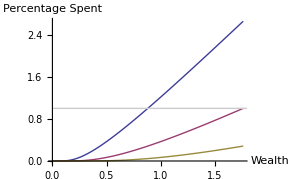

```mathematica
Plot[{g[w,.5]/w,g[w,1]/w,g[w,2]/w},{w,0.001,zz},
AxesLabel->{"Wealth","Percentage Spent"},
Epilog->{GrayLevel[0.8],Line[{{0,1},{1000,1}}]}
]
```

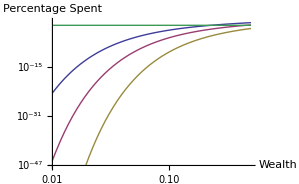

```mathematica
LogLogPlot[{g[w,0.5]/w,g[w,1]/w,g[w,2]/w,0.05},{w,0.01,0.5},
AxesLabel->{"Wealth","Percentage Spent"}
]
```

```mathematica
FullSimplify[σ f[Finv[w/σ]]/. K[δ]->3, {σ>0,w>0,σ/(w-σ)∈ Reals}]
```

(ⅇ^(-(3 σ)/w) w^2)/(3 σ)

Now consider how the recursion tries to find a steady state position. How many rounds of bids until the process falls back to where it was?

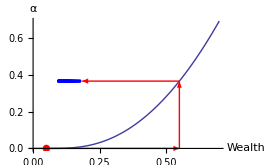

```mathematica
w0=0.05;
w1 =w0+0.5;
x=NestList[(#-g[#])&,w1-g[w1]-g[(w1-g[w1])],50];
Plot[{g[w]},{w,0,0.7},AxesLabel->{"Wealth","α"},
Epilog->{
Red,PointSize[0.02],
Point[{w0,0}],
Arrow[{{w0,0},{w1,0}}],
Arrow[{{w1,0},{w1,g[w1]}}],
Arrow[{{w1,g[w1]},{w1-g[w1],g[w1]}}],
Blue,
PointSize[0.01],
Table[Point[{x⟦i⟧,g[w1]}],{i,1,Length[x]}]
}
]
```

```mathematica
x
```

{0.174812,0.167061,0.160695,0.155339,0.150745,0.146745,0.143219,0.140079,0.137257,0.134702,0.132374,0.13024,0.128274,0.126454,0.124763,0.123187,0.121712,0.120327,0.119024,0.117795,0.116632,0.11553,0.114484,0.113488,0.11254,0.111634,0.110768,0.109939,0.109145,0.108382,0.107649,0.106944,0.106265,0.105611,0.104979,0.104369,0.103779,0.103209,0.102656,0.102121,0.101602,0.101099,0.10061,0.100135,0.0996736,0.0992247,0.0987877,0.0983623,0.0979478,0.0975438,0.0971499}

```mathematica
w1-g[w1]-g[(w1-g[w1])]
```

0.174812

```mathematica
g[w1-g[w1]]
```

0.00974926

```mathematica
PointSize[0.01],
```

```mathematica
0.55-.36543896764980555`
```

```mathematica
g[0.1845610323501945]
```

0.00974926

```mathematica
n=1;
x=w1;
While[x>w0,x=x-g[x];++n]
n
```

2970

## Geometric

Define the geometric density with spending rate ψ and its inverse.  Note that it’s got an ugly inverse function.

```mathematica
Clear[g,K]
g[x_,ψ_]=K+Integrate[-ψ(1-ψ)^(x-1),x]
```

K-((1-ψ)^(-1+x) ψ)/Log[1-ψ]

```mathematica
Clear[h];
h[y_,ψ_]:= 1+(Log[-Log[1-ψ]]-Log[ψ]+Log[y-K])/Log[1-ψ]
```

```mathematica
FullSimplify[h[g[x,ψ],ψ],{x>0,ψ>0, ψ<1}]
```

x

```mathematica
FullSimplify[g[h[x,ψ],ψ],{x>0,ψ>0, ψ<1}]
```

x

For a simpler form, MM pushes terms into the log.

```mathematica
Clear[y,ψ]
FullSimplify[h[y,ψ],{x>0,ψ>0, ψ<1}]
```

Log[-((K-y) (-1+ψ) Log[1-ψ])/ψ]/Log[1-ψ]

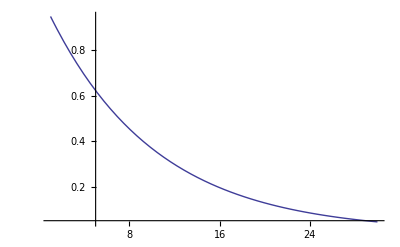

```mathematica
Plot[g[x,0.1],{x,1,30}, PlotRange->All]
```

```mathematica
Finv[f_] :=With[{z=Log[1-ψ]},
Log[f (ψ-1)z/ψ]/z]
f[x_] :=ψ(1-ψ)^(x-1)
```

```mathematica
Finv[w/σ]
```

Log[(w (-1+ψ) Log[1-ψ])/(σ ψ)]/Log[1-ψ]

```mathematica
σ f[Finv[w/σ]]
```

(w (-1+ψ) Log[1-ψ])/(1-ψ)

## Harmonic

```mathematica
Clear[f, Finv];
Finv[f_]:=ⅇ^-f
f[x_] := 1/x
```

Reduces to an exponential (but with wrong sign!)

```mathematica
h[w_,σ_]=σ f[Finv[w/σ]]
```

ⅇ^(w/σ) σ

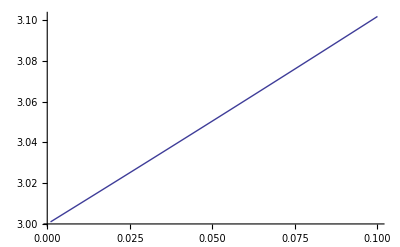

```mathematica
With[{σ=3},
Plot[σ f[Finv[w/σ]],{w,0.001,0.1}]]
```